```mathematica
Clear["Global`*"]
```

```mathematica
(*Funktionen*)
GiveX[l_,y_]:=Extract[l,Position[l,{xs_,ys_}/;ys==y]][[1,1]]
GiveX[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;ys>=Range[[1]]&&ys<=Range[[2]]]][[1,1]]
GiveY[l_,x_]:=Extract[l,Position[l,{xs_,ys_}/;xs==x]][[1,2]]
GiveY[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;xs>=Range[[1]]&&xs<=Range[[2]]]][[1,2]]
GiveXY[l_,z_]:=Extract[l,Position[l,{xs_,ys_,zs_}/;zs==z]][[1]][[{1,2}]]
FindMaximumList[l_]:={GiveX[l,Max[l]],Max[l]}(*Annahme: y>x*)
CheckEq[l1_List,l2_List,n_]:=Sequence[]
CheckEq[l1_List,l2_List,n_]:=l1[[n]]/;(l1[[n,2]]≥l2[[n,2]]&&l1[[n,2]]≤l2[[n+5,2]])||(l1[[n,2]]≤l2[[n,2]]&&l1[[n,2]]≥l2[[n+5,2]])
CheckEqPoints[l1_List,l2_List,start_:1]:=Flatten[Table[{CheckEq[l1,l2,n]},{n,start,Length[l1]-5}]/.{}->Sequence[],1]
```

```mathematica
(*Lösung der DGL*)
s1[L_,r_,h_,x_]:=NDSolve[{i[L,x] θ''[t]==M L1[L,x] h φ''[t]Sin[φ[t]+θ[t]]+M L1[L,x] h φ'[t]^2 Cos[φ[t]+θ[t]]-m L2[L,x] r ψ''[t]Cos[ψ[t]-θ[t]]+m L2[L,x] r ψ'[t]^2 Sin[ψ[t]-θ[t]]+(V[L,x]-λ[t] L2[L,x]) Cos[θ[t]],h φ''[t]==L1[L,x] θ''[t]Sin[φ[t]+θ[t]]+L1[L,x] θ'[t]^2 Cos[φ[t]+θ[t]]-g Sin[φ[t]],r ψ''[t]==-L2[L,x] θ''[t]Cos[ψ[t]-θ[t]]-L2[L,x] θ'[t]^2 Sin[ψ[t]-θ[t]]-(g+λ[t]/m) Cos[ψ[t]],r Sin[ψ[t]-δψ0]+L2[L,x](Sin[θ[t]]-Sin[θ0])==0,θ[0]==θ0,θ'[0]==0,φ[0]==0,φ'[0]==0,ψ[0]==-Pi+δψ0,ψ'[0]==0},{θ,φ,ψ,λ},{t,Tm1,Tp1},Method->{"IndexReduction"->Automatic}]//Quiet
(*Schlinge in der Luft*)
s2[L_,r_,h_,x_]:=NDSolve[{i[L,x] θ''[t]==M L1[L,x] h φ''[t]Sin[φ[t]+θ[t]]+M L1[L,x] h φ'[t]^2 Cos[φ[t]+θ[t]]-m L2[L,x] r ψ''[t]Cos[ψ[t]-θ[t]]+m L2[L,x] r ψ'[t]^2 Sin[ψ[t]-θ[t]]+V[L,x] Cos[θ[t]],h φ''[t]==L1[L,x] θ''[t]Sin[φ[t]+θ[t]]+L1[L,x] θ'[t]^2 Cos[φ[t]+θ[t]]-g Sin[φ[t]],r ψ''[t]==-L2[L,x] θ''[t]Cos[ψ[t]-θ[t]]-L2[L,x] θ'[t]^2 Sin[ψ[t]-θ[t]]-g Cos[ψ[t]],θ[t1]==θ1,θ'[t1]==θs1,φ[t1]==φ1,φ'[t1]==φs1,ψ[t1]==ψ1,ψ'[t1]==ψs1},{θ,φ,ψ},{t,Tm2,Tp2}]
```

```mathematica
Pv[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s2[L,r,h,x];Plot[Evaluate[Sqrt[(L2[L,x] θ'[t])^2+(r ψ'[t])^2+2 L2[L,x]ψ'[t]θ'[t]Cos[ψ[t]-θ[t]]]/.S],{t,Tm2,Tp2},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Geschossgeschwindigkeit",AxesLabel->{"t","v(t)"}]]
Ppsi[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s2[L,r,h,x];Plot[Evaluate[ψ[t]/.S],{t,Tm1,Tp1},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Psi",AxesLabel->{"t","ψ(t)"}]]
Pphi[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s2[L,r,h,x];Plot[Evaluate[φ[t]/.S],{t,Tm1,Tp1},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Phi",AxesLabel->{"t","ψ(t)"}]]
Pth[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s2[L,r,h,x];Plot[Evaluate[θ[t]/.S],{t,Tm1,Tp1},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Theta",AxesLabel->{"t","θ(t)"}]]
Plam[L_,r_,h_,x_,t1_:0]:=Block[{S},S=s1[L,r,h,x];Plot[Evaluate[λ[t]/.S],{t,Tm1,Tp1},PlotRange->All,GridLines->{{{t1,Red}},None},PlotLabel->"Lambda",AxesLabel->{"t","λ(t)"}]]
```

```mathematica
(*Listen und Funktionen für das erste Intervall*)
lamList1[L_,r_,h_,x_]:=Block[{S},S=s1[L,r,h,x];Table[{t,(λ[t]/.S)[[1]]},{t,Tm1,Tp1,(Tp1-Tm1)/n}]]
tlv[L_,r_,h_,x_]:=GiveX[lamList1[L,r,h,x],{-0.1,0}]
SetInitial2[L_,r_,h_,x_]:=Block[{S},S=s1[L,r,h,x];
θ1=(θ[t1]/.S)[[1]];
θs1=(θ'[t1]/.S)[[1]];
φ1=(φ[t1]/.S)[[1]];
φs1=(φ'[t1]/.S)[[1]];
ψ1=(ψ[t1]/.S)[[1]];
ψs1=(ψ'[t1]/.S)[[1]];
]
```

```mathematica
(*Listen und Funktionen für das zweite Intervall*)
thList2[L_,r_,h_,x_]:=Block[{S},
SetInitial2[L,r,h,x];
S=s2[L,r,h,x];
Table[{t,(θ[t]/.S)[[1]]},{t,Tm2,Tp2,(Tp2-Tm2)/n}]]
psiList2[L_,r_,h_,x_]:=Block[{S},
SetInitial2[L,r,h,x];
S=s2[L,r,h,x];
Table[{t,(ψ[t]/.S)[[1]]},{t,Tm2,Tp2,(Tp2-Tm2)/n}]]
phiList2[L_,r_,h_,x_]:=Block[{S},
SetInitial2[L,r,h,x];
S=s2[L,r,h,x];
Table[{t,(φ[t]/.S)[[1]]},{t,Tm2,Tp2,(Tp2-Tm2)/n}]]
(*Betrag der Geschossgeschwindigkeit*)
vList[L_,r_,h_,x_]:=Block[{S},
SetInitial2[L,r,h,x];
S=s2[L,r,h,x];
Table[{t,Re[(Sqrt[(L2[L,x] θ'[t])^2+(r ψ'[t])^2+2 L2[L,x]ψ'[t]θ'[t]Cos[ψ[t]-θ[t]]]/.S)[[1]]]},{t,Tm2,Tp2,(Tp2-Tm2)/n}]]
(*x-Komponente der Geschossgeschwindigkeit*)
vxList[L_,r_,h_,x_]:=Block[{S},
SetInitial2[L,r,h,x];
S=s2[L,r,h,x];
Table[{t,(-L2[L,x] Sin[θ[t]] θ'[t]-r Sin[ψ[t]] ψ'[t]/.S)[[1]]},{t,Tm2,Tp2,(Tp2-Tm2)/n}]]
(*y-Komponente der Geschossgeschwindigkeit*)
vyList[L_,r_,h_,x_]:=Block[{S},
SetInitial2[L,r,h,x];
S=s2[L,r,h,x];
Table[{t,(L2[L,x] Cos[θ[t]] θ'[t]+r Cos[ψ[t]] ψ'[t]/.S)[[1]]},{t,Tm2,Tp2,(Tp2-Tm2)/n}]]
(*Integrierte Wurfweite*)
sWurf[vx_,vy_,h_]:=vx(vy+Sqrt[2 g h +vy^2])/g
sWurfList[L_,r_,h_,x_]:=Block[{S,vx,vy,H},
SetInitial2[L,r,h,x];
S=s2[L,r,h,x];
vx=((-L2[L,x] Sin[θ[t]] θ'[t]-r Sin[ψ[t]] ψ'[t])/.S)[[1]];
vy=((L2[L,x] Cos[θ[t]] θ'[t]+r Cos[ψ[t]] ψ'[t])/.S)[[1]];
H=((L Sin[θ[t]]+h)/.S)[[1]];
Table[{t,Re[sWurf[vx,vy,H]]},{t,Tm2,Tp2,(Tp2-Tm2)/n}]]
tmax[L_,r_,h_,x_]:=FindMaximumList[Abs[sWurfList[L,r,h,x]]][[1]]
smax[L_,r_,h_,x_]:=GiveY[sWurfList[L,r,h,x],tmax[L,r,h,x]]
vmax[L_,r_,h_,x_]:=GiveY[vList[L,r,h,x],tmax[L,r,h,x]]
```

```mathematica
(*theoretisch maximale Wurfweite und Effizienz*)
v[L_,h_,x_]:=Sqrt[2M g L1[L,x](1+Sin[Abs[θ0]])/m];
stheo[L_,r_,h_,x_]:=sWurf[v[L,h,x]/Sqrt[2],v[L,h,x]/Sqrt[2],h+L+r/Sqrt[2]]
Efficiency[L_,r_,h_,x_]:=Abs[smax[L,r,h,x]/stheo[L,r,h,x]]
```

```mathematica
(*reales Trägheitsmoment eines spitz zulaufenden Balkens, Δ ist die Verschiebung relativ zu h/2*)
(*a,b sind die Abmessungen am unteren Ende, c,d die Abmessungen an der Wurfarmspitze*)
(*positives Δ meint hier Verschiebung,dass die Strecke Drehachse-Gegengewicht kleiner und die Strecke Drehachse-Geschoss größer wird (umgekehrt zur Definition in Trägheitsmoment.nb)*)
iw[h_,Δ_]:=(h*(a*(4*b^3+3*b^2*d+2*b*d^2+d^3+8*b*h^2+2*d*h^2-40*b*h*Δ+40*(2*b+d)*Δ^2)+c*(b^3+2*b^2*d+3*b*d^2+4*d^3+2*b*h^2+8*d*h^2+40*d*h*Δ+40*(b+2*d)*Δ^2))*ρ)/240
(*Entfernung Schwerpunkt-Drehachse*)
sp[h_,Δ_]:=-((a*b*h-c*d*h-4*a*b*Δ-2*b*c*Δ-2*a*d*Δ-4*c*d*Δ)/(4*a*b+2*b*c+2*a*d+4*c*d))
(*Volumen*)
vol[h_]:=(a (2 b+d)+c (b+2 d)) h/6
```

```mathematica
(*abgeleitete Parameter*)
L1[L_,x_]:=L/2-x
L2[L_,x_]:=L/2+x
μ[L_]:=vol[L] ρ
V[L_,x_]:=M g L1[L,x] - m g L2[L,x] - μ[L]sp[L,x]g
i[L_,x_]:=iw[L,x]+m L2[L,x]^2+M L1[L,x]^2
```

```mathematica
(*Parameter*)
M=50.; (*Masse des Gegengewichts*)
m=0.5; (*Masse des Geschosses, guter Start M/100*)
Tm1=0.0;(*Zeitintervall Schlinge auf dem Boden*)
Tp1=0.15;
Tm2=0.0;(*Zeitintervall Wurf, Tm2 wird später automatisch bestimmt Tm2->t1*)
Tp2=1.0;
θ0=-Pi/3; (*Startwinkel des Wurfarms, wenn keine Einschränkung aus Geometrie*)
δψ0=0.0;(*0.48, Falls die Höhe des Trebuchets nicht mit L2 Sin[45°] übereinstimmt*)
n=2000;(*Anzahl der Auswertungspunkte*)
(*Konstanten*)
g=9.81;
(*Dichte Holz*)
ρ=670.;(*670kg/m^3*)
(*Abmessungen des Wurfarms*)
a=0.1;
b=0.1;
c=0.05;
d=0.05;
(*Startwerte*)
L0=2.03(*Länge des Wurfarms*)
r0=1.13(*Länge der Schlinge, guter Start L2*)
h0=0.36(*Länge der Aufhängung des Gegengewichts, guter Start: L0/4*)
x0=0.41(*Abstand Aufhängung des Wurfarms zu h/2, guter Start: L0/4.5. Positive x0 meint, dass die Strecke Drehachse-Gegengewicht kleiner und die Strecke Drehachse-Geschoss größer wird.*)
```

2.03

1.13

0.36

0.41

0.1455

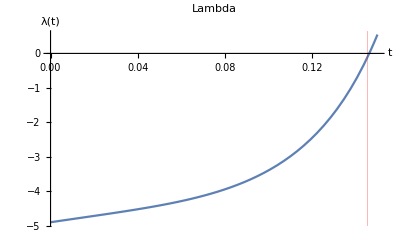

-0.566101

3.82568

-0.0087008

0.469725

-2.71283

4.47706

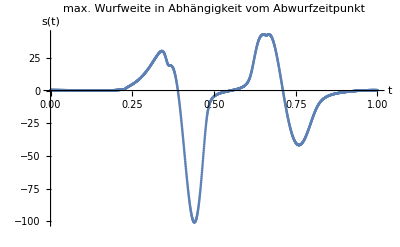

```mathematica
(*Löse zuerst die erste DGL, um den Zeitpunkt zu finden, wann das Geschoss den Boden verlässt -> λ=0*)
t1=tlv[L0,r0,h0,x0]
Plam[L0,r0,h0,x0,t1]
(*finde dann die Anfangsbedingungen für die zweite DGL*)
SetInitial2[L0,r0,h0,x0]
θ1
θs1
φ1
φs1
ψ1
ψs1
ListPlot[sWurfList[L0,r0,h0,x0],PlotRange->All,PlotLabel->"max. Wurfweite in Abhängigkeit vom Abwurfzeitpunkt",AxesLabel->{"t","s(t)"}]
```

0.44

-100.63

0.439558

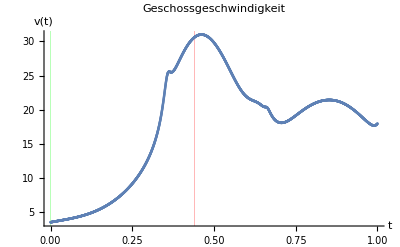

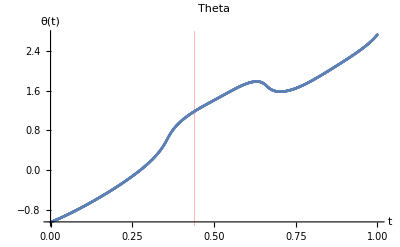

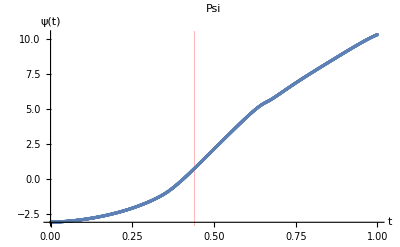

```mathematica
t2=tmax[L0,r0,h0,x0]
smax[L0,r0,h0,x0]
Efficiency[L0,r0,h0,x0]
Show[Pv[L0,r0,h0,x0,t2],ListPlot[vList[L0,r0,h0,x0]]]
Show[Pth[L0,r0,h0,x0,t2],ListPlot[thList2[L0,r0,h0,x0]]]
Show[Ppsi[L0,r0,h0,x0,t2],ListPlot[psiList2[L0,r0,h0,x0]]]
```

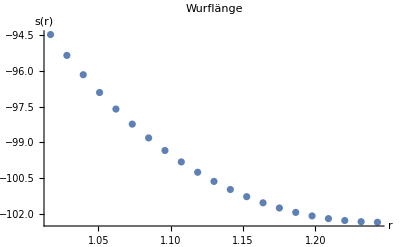

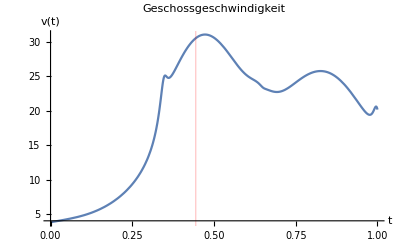

Abwurfzeitpunkt t2 = 0.4445

neuer Startwert für L0 = 2.03

neuer Startwert für r0 = 1.243

neuer Startwert für h0 = 0.36

neuer Startwert für x0 = 0.41

vmax = 30.5644

smax = -102.336

Effizienz = 0.44686

```mathematica
(*1D Analyse in r*)
smaxr=Table[{r,smax[L0,r,h0,x0]},{r,0.9r0,1.1r0,0.1r0/10}];
ListPlot[smaxr,PlotLabel->"Wurflänge",AxesLabel->{"r","s(r)"}]
rmax=FindMaximumList[Abs[smaxr]][[1]];
r0=rmax;
t2=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t2]
Print["Abwurfzeitpunkt t2 = ",t2]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
Print["Effizienz = ",Efficiency[L0,r0,h0,x0]]
```

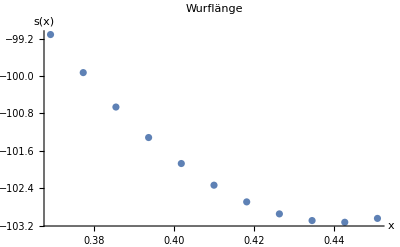

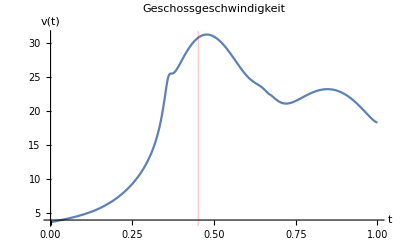

Abwurfzeitpunkt t0 = 0.4515

neuer Startwert für L0 = 2.03

neuer Startwert für r0 = 1.243

neuer Startwert für h0 = 0.36

neuer Startwert für x0 = 0.4428

vmax = 30.703

smax = -103.129

Effizienz = 0.475757

```mathematica
(*1D Analyse in x*)
smaxx=Table[{x,smax[L0,r0,h0,x]},{x,0.9x0,1.1 x0,0.2x0/10}];
ListPlot[smaxx,PlotLabel->"Wurflänge",AxesLabel->{"x","s(x)"}]
xmax=FindMaximumList[Abs[smaxx]][[1]];
x0=xmax;
t2=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t2]
Print["Abwurfzeitpunkt t0 = ",t2]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
Print["Effizienz = ",Efficiency[L0,r0,h0,x0]]
```

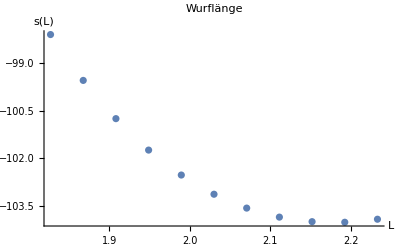

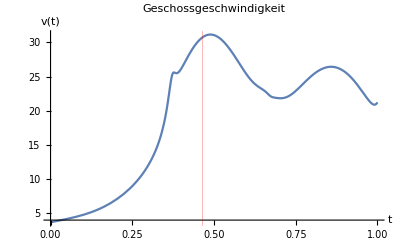

Abwurfzeitpunkt t0 = 0.465

neuer Startwert für L0 = 2.1924

neuer Startwert für r0 = 1.243

neuer Startwert für h0 = 0.36

neuer Startwert für x0 = 0.4428

vmax = 30.7287

smax = -104.01

Effizienz = 0.420689

```mathematica
(*1D Analyse in L*)
smaxL=Table[{L,smax[L,r0,h0,x0]},{L,0.9L0,1.1 L0,0.2L0/10}];
ListPlot[smaxL,PlotLabel->"Wurflänge",AxesLabel->{"L","s(L)"}]
Lmax=FindMaximumList[Abs[smaxL]][[1]];
L0=Lmax;
t2=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t2]
Print["Abwurfzeitpunkt t0 = ",t2]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
Print["Effizienz = ",Efficiency[L0,r0,h0,x0]]
```

```mathematica
(*Notiz: Optimierung über h konvergiert nicht. h sollte deshalb so groß wie technisch möglich gewählt werden.*)
(*1D Analyse in h*)
(*smaxh=Table[{h,smax[L0,r0,h,x0]},{h,0.9h0,1.1 h0,0.2h0/10}];
ListPlot[smaxh,PlotLabel->"Wurflänge",AxesLabel->{"h","s(h)"}]
hmax=FindMaximumList[Abs[smaxh]][[1]];
h0=hmax;
t2=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t2]
Print["Abwurfzeitpunkt t0 = ",t2]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]*)
```

```mathematica
(*Vektoren*)
r1List1[L_,r_,h_,x_]:=Block[{S},S=s1[L,r,h,x];Table[{((L2[L,x]Cos[θ[t]])/.S)[[1]],((L2[L,x]Sin[θ[t]])/.S)[[1]]},{t,Tm1,t1,0.01}]]
r1List2[L_,r_,h_,x_]:=Block[{S},S=s2[L,r,h,x];Table[{((L2[L,x]Cos[θ[t]])/.S)[[1]],((L2[L,x]Sin[θ[t]])/.S)[[1]]},{t,t1,t2,0.01}]]
r1List[L_,r_,h_,x_]:=Join[r1List1[L,r,h,x],r1List2[L,r,h,x]]
r2List1[L_,r_,h_,x_]:=Block[{S},S=s1[L,r,h,x];Table[{((L2[L,x]Cos[θ[t]]+r Cos[ψ[t]])/.S)[[1]],((L2[L,x]Sin[θ[t]]+r Sin[ψ[t]])/.S)[[1]]},{t,Tm1,t1,0.01}]]
r2List2[L_,r_,h_,x_]:=Block[{S},S=s2[L,r,h,x];Table[{((L2[L,x]Cos[θ[t]]+r Cos[ψ[t]])/.S)[[1]],((L2[L,x]Sin[θ[t]]+r Sin[ψ[t]])/.S)[[1]]},{t,t1,t2,0.01}]]
r2List[L_,r_,h_,x_]:=Join[r2List1[L,r,h,x],r2List2[L,r,h,x]]
r3List1[L_,r_,h_,x_]:=Block[{S},S=s1[L,r,h,x];Table[{((-L1[L,x]Cos[θ[t]])/.S)[[1]],((-L1[L,x]Sin[θ[t]])/.S)[[1]]},{t,Tm1,t1,0.01}]]
r3List2[L_,r_,h_,x_]:=Block[{S},S=s2[L,r,h,x];Table[{((-L1[L,x]Cos[θ[t]])/.S)[[1]],((-L1[L,x]Sin[θ[t]])/.S)[[1]]},{t,t1,t2,0.01}]]
r3List[L_,r_,h_,x_]:=Join[r3List1[L,r,h,x],r3List2[L,r,h,x]]
r4List1[L_,r_,h_,x_]:=Block[{S},S=s1[L,r,h,x];Table[{((-L1[L,x]Cos[θ[t]]-h Sin[φ[t]])/.S)[[1]],((-L1[L,x]Sin[θ[t]]-h Cos[φ[t]])/.S)[[1]]},{t,Tm1,t1,0.01}]]
r4List2[L_,r_,h_,x_]:=Block[{S},S=s2[L,r,h,x];Table[{((-L1[L,x]Cos[θ[t]]-h Sin[φ[t]])/.S)[[1]],((-L1[L,x]Sin[θ[t]]-h Cos[φ[t]])/.S)[[1]]},{t,t1,t2,0.01}]]
r4List[L_,r_,h_,x_]:=Join[r4List1[L,r,h,x],r4List2[L,r,h,x]]
Manipulate[
Show[ListPlot[{r2List[L0,r0,h0,x0],r1List[L0,r0,h0,x0]},PlotRange->{{-L2[L0,x0]-r0,L2[L0,x0]+r0},{-L2[L0,x0]-r0,L2[L0,x0]+r0}},Frame->True,ImageSize->{600,600},AspectRatio->1],Graphics[Line[{r4List[L0,r0,h0,x0][[Round[n]]],r3List[L0,r0,h0,x0][[Round[n]]],{0,0},r1List[L0,r0,h0,x0][[Round[n]]],r2List[L0,r0,h0,x0][[Round[n]]]}]]],{n,1,Length[r1List[L0,r0,h0,x0]]}]
```

```mathematica
L0/20*100
r0/20*100
h0/20*100
x0/20*100
H0=L2[L0,x0]Sin[45°];
H0/20*100
```

10.962

6.215

1.8

2.214

5.44119

```mathematica
L1[L0,x0]/20*100
L2[L0,x0]/20*100
```

3.267

7.695

```mathematica
L1[L0,x0]
L2[L0,x0]
H0
L1[L0,x0]+h0
```

0.6534

1.539

1.08824

1.0134

```mathematica
(*Winkel ψ0, der daraus resultiert, wenn H0≠ L2 Sin[θ0]*)
cbox=0.36;
ArcSin[(L1[L0,x0]+h0+cbox/2-H0)/r0]
```

0.0847052

```mathematica
1.5/5
```

0.3

```mathematica
0.8/5
```

0.16